```mathematica
Needs["ErrorBarPlots`"];
Needs["PlotLegends`"];
```

```mathematica
<<MaTeX`
```

```mathematica
texStyle={FontFamily->"Helvetica",FontSize->20};
```

### Group invariants - Sp(N)

```mathematica
(*dimension of group representation, second column of Table.V in arXiv:2001.02690*)
dA[n_]:=(n(n+1))/2;
```

```mathematica
(*normalization for the representation, third column of Table.V in arXiv:2001.02690*)
Tf[n_]:=1/2;
TF[n_]:=(n-2)/2;
```

```mathematica
(*eigenvalue of qadratic Casimir operators, forth column of Table.V in arXiv:2001.02690*)
Cf[n_]:=(n+1)/4;
CA[n_]:=(n+2)/2;
CF[n_]:=n/2;
```

```mathematica
(*quadratic group invaraints, fifth column of Table.V in arXiv:2001.02690*)
```

```mathematica
(*group invariants by contracting symmetric tensors, Eq.(A3) in arXiv:2001.02690, where Eq. (A2) and group factors in Table. V and VI have been used to obatain the following results*)
dff[n_]:=1/384 (4+n+n^2);
dfA[n_]:=1/384 (2+n) (22+7 n+n^2);
dFf[n_]:=1/384 (-2+n) (10-5 n+n^2);
dAA[n_]:=1/384 (2+n) (296+138 n+15 n^2+n^3);
dFF[n_]:=1/384 (-2+n) (-104+110 n-13 n^2+n^3);
dFA[n_]:=1/384 (-2+n) (2+n) (28+n+n^2);
```

### Anomalous dimension - coefficients for two-representation gauge theory (used only for the estimation of the conformal window using BZ expansion)

```mathematica
DF[n_,n2_]:=CA[n](7CA[n]+11CF[n])+4 n2 Tf[n] (Cf[n]-CF[n]);(*Eq. (3.1) in arXiv:1809.02242*)
```

```mathematica
AF0[n_]:=CA[n] (3 CA[n] TF[n]^2 (-18473 CA[n]^4+144004 CA[n]^3 CF[n]+650896 CA[n]^2 CF[n]^2+356928 CA[n] CF[n]^3+569184 CF[n]^4)+2^7 (DF[n,0]/CA[n]) (-20 TF[n]^2 dAA[n]+352 CA[n] TF[n] dFA[n]-1331 CA[n]^2 dFF[n])+33 (2^10) (DF[n,0]/CA[n]) Zeta[3] (2 TF[n]^2 dAA[n]-13 CA[n] TF[n] dFA[n]+11 CA[n]^2 dFF[n]));(*Eq. (3.7) in arXiv:1809.02242*)
```

```mathematica
AF1[n_]:=CA[n] TF[n]^2 Tf[n] (273840 CA[n]^3 (Cf[n]-CF[n])+CA[n]^2 (-1511040 CF[n]^2+1916256 CF[n] Cf[n]-405216 Cf[n]^2)+CA[n] (-129600 CF[n]^3+522432 CF[n]^2 Cf[n]-485568 CF[n] Cf[n]^2+92736 Cf[n]^3)+CF[n] (-1241856 CF[n]^3+1020096 CF[n]^2 Cf[n]+76032 CF[n] Cf[n]^2+145728 Cf[n]^3))+10240 TF[n]^2 Tf[n] (CF[n]-Cf[n]) dAA[n]+CA[n] TF[n] Tf[n] (-114688 CA[n]-360448 CF[n]+180224 Cf[n]) dFA[n]+CA[n] TF[n]^2 (114688 CA[n]+180224 CF[n]) dfA[n]+CA[n]^2 Tf[n] (867328 CA[n]+2044416 CF[n]-681472 Cf[n]) dFF[n]+
CA[n]^2 TF[n](-867328 CA[n]-1362944 CF[n]) dFf[n]+Zeta[3] (270336 TF[n]^2 Tf[n] (Cf[n]-CF[n]) dAA[n]+
CA[n] TF[n] Tf[n] (1118208 CA[n]+3514368 CF[n]-1757184 Cf[n]) dFA[n]+CA[n] TF[n]^2 (-1118208 CA[n]-1757184 CF[n]) dfA[n]+
CA[n]^2 Tf[n] (-1892352 CA[n]-4460544 CF[n]+1486848 Cf[n]) dFF[n]+CA[n]^2 TF[n] (1892352 CA[n]+2973696 CF[n]) dFf[n]);(*Eq. (3.8) in arXiv:1809.02242*)
```

```mathematica
AF2[n_]:=TF[n]^2 Tf[n]^2 (350976 CA[n]^2 (CF[n]-Cf[n])^2+CA[n] (-94464 CF[n]^3-2304 CF[n]^2 Cf[n]+288000CF[n] Cf[n]^2
-191232 Cf[n]^3)+225792 CF[n]^4-370944 CF[n]^3 Cf[n]+119808 CF[n]^2 Cf[n]^2-29952 CF[n] Cf[n]^3+55296 Cf[n]^4)+2^(16) TF[n] Tf[n] (CF[n]-Cf[n]) (Tf[n] dFA[n]-TF[n] dfA[n])+CA[n] Tf[n]^2 (-157696 CA[n]+495616 Cf[n]-743424 CF[n]) dFF[n]+CA[n] TF[n] Tf[n] (315392 CA[n]+991232 CF[n]-495616 Cf[n]) dFf[n]+CA[n] TF[n]^2 (-157696 CA[n]-247808 CF[n]) dff[n]+
Zeta[3] (638976 TF[n] Tf[n] (CF[n]-Cf[n]) (TF[n] dfA[n]-Tf[n] dFA[n])+CA[n] Tf[n]^2 (344064 CA[n]+1622016 CF[n]-1081344 Cf[n]) dFF[n]+CA[n] TF[n] Tf[n](-688128 CA[n]-2162688 CF[n]+1081344 Cf[n]) dFf[n]+CA[n] TF[n]^2 (344064 CA[n]+540672 CF[n])dff[n]);(*Eq. (3.9) in arXiv:1809.02242*)
```

```mathematica
AF3[n_]:=2^(13) Tf[n] (CF[n]-Cf[n]) (11-24 Zeta[3]) (Tf[n]^2 dFF[n]-2 TF[n] Tf[n] dFf[n]+TF[n]^2 dff[n]);
```

```mathematica
KF1[n_,n2_]:=(8 CF[n] TF[n])/DF[n,n2];(*Eq. (3.4) in arXiv:1809.02242*)
```

```mathematica
KF2[n_,n2_]:=((4 CF[n] TF[n]^2)/(3DF[n,n2]^3)) (CA[n](7CA[n]+4CF[n])(5CA[n]+88CF[n])+(2^4) n2 Tf[n] (Cf[n]-CF[n]) (10 CA[n]+8 CF[n]+Cf[n]));(*Eq. (3.5) in arXiv:1809.02242*)
```

```mathematica
KF3[n_,n2_]:=((4 CF[n] TF[n])/(3^4 DF[n,n2]^5)) (AF0[n]+AF1[n] n2+AF2[n] n2^2+AF3[n] n2^3);(*Eq. (3.6) in arXiv:1809.02242*)
```

```mathematica
NAF[n_,n2_]:=(11 CA[n]-4 n2 Tf[n])/(4 TF[n]);(*Eq. (2.5) in arXiv:1809.02242*)
```

```mathematica
DNF[n_,n1_,n2_]:=(NAF[n,n2]-n1);(*Eq. (1.2) in arXiv:1809.02242*)
```

### Analytical estimation of the conformal window

```mathematica
nc=4;(*number of colour*)
```

```mathematica
xticks={{0,MaTeX["0",Magnification->1.8],{0,0.01}},{2,MaTeX["2",Magnification->1.8],{0,0.01}},{4,MaTeX["4",Magnification->1.8],{0,0.01}},{6,MaTeX["6",Magnification->1.8],{0,0.01}},{8,MaTeX["8",Magnification->1.8],{0,0.01}},{10,MaTeX["10",Magnification->1.8],{0,0.01}},{12,MaTeX["12",Magnification->1.8],{0,0.01}},{14,MaTeX["14",Magnification->1.8],{0,0.01}},{16,MaTeX["16",Magnification->1.8],{0,0.01}}};
(*for the plot axis*)
yticks={{0,MaTeX["0",Magnification->1.8],{0,0.01}},{1,MaTeX["1",Magnification->1.8],{0,0.01}},{2,MaTeX["2",Magnification->1.8],{0,0.01}},{3,MaTeX["3",Magnification->1.8],{0,0.01}},{4,MaTeX["4",Magnification->1.8],{0,0.01}},{5,MaTeX["5",Magnification->1.8],{0,0.01}},{6,MaTeX["6",Magnification->1.8],{0,0.01}},{7,MaTeX["7",Magnification->1.8],{0,0.01}},{8,MaTeX["8",Magnification->1.8],{0,0.01}}};(*for the plot axis*)
```

#### upper bound from 1-loop beta function

```mathematica
boundAF[n_,n1_,n2_]:=n1 TF[n]+n2 Tf[n]-11 CA[n]/4;(*Eq. (2) in arXiv:2001.02690 up to an unimportant prefactor*)
```

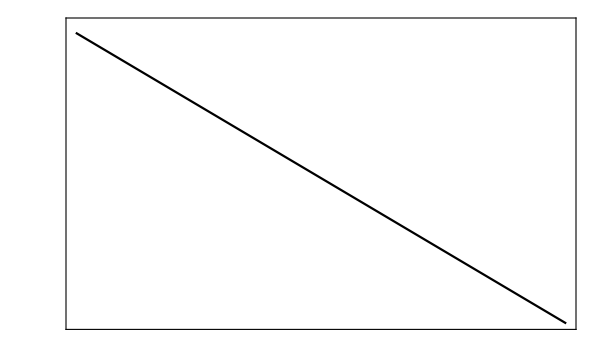

```mathematica
xmin=0;
xmax=16.5;
ymin=0;
ymax=8.5;
boundAFplot=ContourPlot[{boundAF[nc,x,y]==0},{y,0,25},{x,0,25},PlotRange->{{xmin,xmax},{ymin,ymax}},Frame->True,AxesStyle->Thick,AxesStyle->Black,FrameStyle->Black,FrameLabel->{MaTeX["N_{\\rm f}",Magnification->1.8],MaTeX["N_{\\rm as}",Magnification->1.8]},FrameTicks->{{yticks,None},{xticks,None}},ContourStyle->{Black},BaseStyle->texStyle,ImageSize->600,AspectRatio->3/5]
```

#### lower bound from 2-loop beta function

```mathematica
twoloopbeta[n_,n1_,n2_]:=n1 TF[n] (5 CA[n]+3 CF[n])+n2 Tf[n] (5 CA[n]+3 Cf[n])-17 CA[n]^2/2;(*Eq. (2) in arXiv:2001.02690 up to an unimportant prefactor*)
```

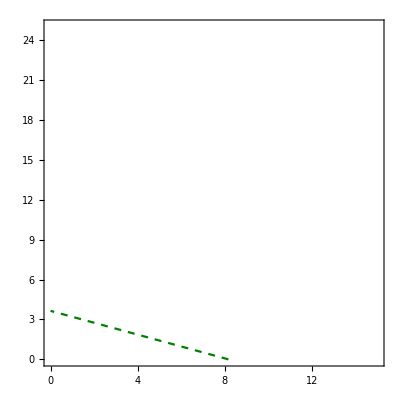

```mathematica
twoloopbetaplot=ContourPlot[{twoloopbeta[nc,x,y]==0},{y,0,15},{x,0,25},ContourStyle->{Dashed,RGBColor[0,.5,0]}]
```

#### lower bound from Schwinger-Dyson approach

```mathematica
b1[n_,n1_,n2_]:=(11 CA[n]-4 (n1 TF[n]+n2 Tf[n]))/3;(*Eq. (2) in arXiv:2001.02690*)
SD[n_,n1_,n2_]:=(4 π) (b1[n,n1,n2]/((-4/3) twoloopbeta[n,n1,n2]))+π/(3 CF[n]);(*equating Eq. (5) and (7) in arXiv:2001.02690*)
```

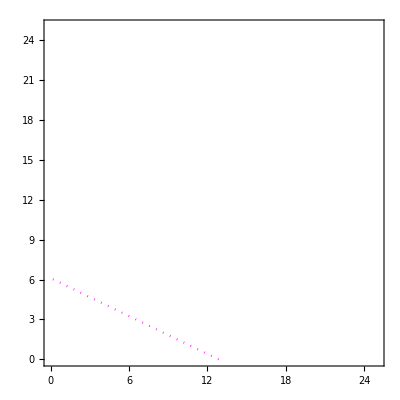

```mathematica
SDplot=ContourPlot[{SD[nc,x,y]==0},{y,0,25},{x,0,25},ContourStyle->{Dotted,RGBColor[1,0,1]}]
```

#### lower bound from the all-order beta function

```mathematica
NSVZ1[n_,n1_,n2_]:=11 CA[n]-6 (n1 TF[n]+n2 Tf[n]);(*Eq. (11) in arXiv:2001.02690 with γ=1*)
```

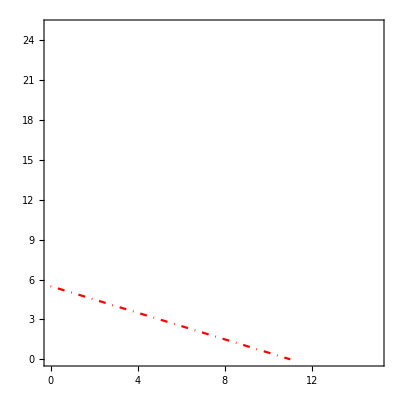

```mathematica
NCVZplot=ContourPlot[{NSVZ1[nc,x,y]==0},{y,0,15},{x,0,25},ContourStyle->{DotDashed,Red}]
```

#### lower bound from the BZ exansion

```mathematica
GIR1[n_,n1_,n2_]:=2 KF1[n,n2] DNF[n,n1,n2];(*LO, Eq. (29) in arXiv:2001.02690*)
GIR2[n_,n1_,n2_]:=2 KF1[n,n2] DNF[n,n1,n2]+(2 KF2[n,n2]-KF1[n,n2]^2) DNF[n,n1,n2]^2;(*NLO, Eq. (30) in arXiv:2001.02690*)
GIR3[n_,n1_,n2_]:=2 KF1[n,n2] DNF[n,n1,n2]+(2 KF2[n,n2]-KF1[n,n2]^2) DNF[n,n1,n2]^2+(2 KF3[n,n2]-2 KF1[n,n2] KF2[n,n2]) DNF[n,n1,n2]^3;(*NNLO, Eq. (31) in arXiv:2001.02690*)
```

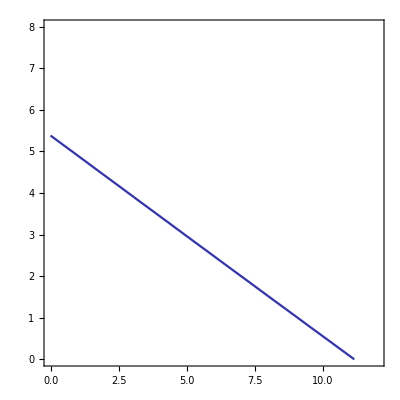

```mathematica
Gamma3loopplot=ContourPlot[{GIR3[nc,x,y]==1},{y,0,12},{x,0,8},ContourStyle->{RGBColor[.2,.2,.7]}](*Eq. (28) in arXiv:2001.02690*)
```

#### Final plot for the conformal window

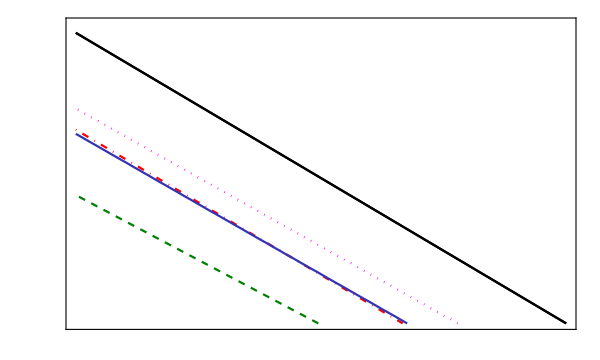

```mathematica
Show[{boundAFplot,twoloopbetaplot,NCVZplot,SDplot,boundAFplot,Gamma3loopplot}]
```